## Double Pendulum with Damping

### Problem Description

A compound double pendulum is released from rest in the following shape.

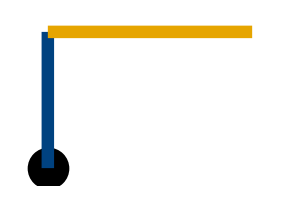

```mathematica
With[{L1=1,m1=1,L2=1,m2=1},Module[{pendulum1,pendulum2},
pendulum1=Line[{{0,0},{L1 Sin[θ1],-L1 Cos[θ1]}}]/.{θ1->180 Degree};
pendulum2=Line[{{L1 Sin[θ1],-L1 Cos[θ1]},{L1 Sin[θ1]+L2 Sin[θ2],-L1 Cos[θ1]-L2 Cos[θ2]}}]/.{θ1->180Degree,θ2->90Degree};
Graphics[
{
{PointSize[0.1],Point[{0,0}]},
{Thickness[0.03],ColorData[81,"ColorList"][[1]],pendulum1},
{Thickness[0.03],ColorData[81,"ColorList"][[2]],pendulum2}
},
PlotRange->{{-0.1,1.1},{-0.1,1.1}},
Frame->False
,ImageSize->{300,200},ImagePadding->None]]]
```

It is then subject to gravity and a frictional force modeled as f=c θ̇, where c is chosen to be 0.008.
Masses and lengths are set to be equal to unity, with g = 9.81.

### Solve the system and plot the results.

```mathematica
Module[{eq1,eq2,T,V,Ξ1,Ξ2,v1,v2,r1,r2,L,sol,pendulum1,pendulum2,tfinal,max,min},
r1[θ1_,θ2_]:={L1/2 Sin[θ1],-L1/2 Cos[θ1]};
r2[θ1_,θ2_]:={L1 Sin[θ1]+L2/2 Sin[θ2],-L1 Cos[θ1]-L2/2 Cos[θ2]};
v1=D[r1[θ1[t],θ2[t]],t];
v2=D[r2[θ1[t],θ2[t]],t];
V=m1 g r1[θ1[t],θ2[t]][[2]]+m2 g r2[θ1[t],θ2[t]][[2]] ;(*m g y *)
T=1/2 m1 Dot[v1,v1]+1/2 m2 Dot[v2,v2];
Ξ1=-c θ1'[t];
Ξ2=-c θ2'[t];
L=T-V;
eq1=D[D[L,θ1'[t]],t]-D[L,θ1[t]]==Ξ1;
eq2=D[D[L,θ2'[t]],t]-D[L,θ2[t]]==Ξ2;
tfinal=10;
sol=With[{rules={g->9.81}},ParametricNDSolve[{eq1/.rules,eq2/.rules,θ1[0]==θ10,θ2[0]==θ20,θ1'[0]==0,θ2'[0]==0},{θ1,θ2,θ1',θ2'},{t,0,tfinal},{L1,m1,L2,m2,c,θ10,θ20}]];
Manipulate[With[{L1=1,m1=1,L2=1,m2=1,θmax=5 360,θmin=-3 360},
Column@{Manipulate[
Row@{Show[ListPlot[{({Mod[θ1[L1,m1,L2,m2,c,θ10,θ20][t]/.sol,2π,-π],θ1'[L1,m1,L2,m2,c,θ10,θ20][t]/.sol}/.t->#)&/@Range[0,tf,0.002],
({Mod[θ2[L1,m1,L2,m2,c,θ10,θ20][t]/.sol,2π,-π],θ2'[L1,m1,L2,m2,c,θ10,θ20][t]/.sol}/.t->#)&/@Range[0,tf,0.002]
},
Frame->True,
PlotStyle->ColorData[81,"ColorList"],
PlotRange->{{-π,π},{-20,20}},
ImageSize->{600,400}],
ListPlot[
{
{{Mod[θ1[L1,m1,L2,m2,c,θ10,θ20][t],2π,-π],θ1'[L1,m1,L2,m2,c,θ10,θ20][t]}/.sol/.t->tf},{{Mod[θ2[L1,m1,L2,m2,c,θ10,θ20][t],2π,-π],θ2'[L1,m1,L2,m2,c,θ10,θ20][t]}/.sol/.t->tf}
},
PlotStyle->ColorData[81,"ColorList"],
PlotMarkers->{"OpenMarkers", Medium}
]
],
Module[{},
pendulum1=Line[{{0,0},{L1 Sin[θ1],-L1 Cos[θ1]}}]/.{θ1->θ1[L1,m1,L2,m2,c,θ10,θ20][t]}/.sol;
pendulum2=Line[{{L1 Sin[θ1],-L1 Cos[θ1]},{L1 Sin[θ1]+L2 Sin[θ2],-L1 Cos[θ1]-L2 Cos[θ2]}}]/.{θ1->θ1[L1,m1,L2,m2,c,θ10,θ20][t],θ2->θ2[L1,m1,L2,m2,c,θ10,θ20][t]}/.sol;
Graphics[
{
{PointSize[0.01],Point[{0,0}]},
{Thickness[0.01],ColorData[81,"ColorList"][[1]],pendulum1},
{Thickness[0.01],ColorData[81,"ColorList"][[2]],pendulum2}
}/.t->tf,
PlotRange->{{-(L1+L2),(L1+L2)},{-(L1+L2),(L1+L2)}},
Frame->False
,ImageSize->{300,200}]]},
{{tf,0.05,"Time "},0.05,tfinal}
],
Plot[{1/Degree θ1[L1,m1,L2,m2,c,θ10,θ20][t]/.sol,1/Degree θ2[L1,m1,L2,m2,c,θ10,θ20][t]/.sol},{t,0,tfinal},
ImageSize->{900,200},
AspectRatio->Full,
Ticks->{Automatic,Range[θmin,θmax,90]},
GridLines->{Automatic,Range[θmin,θmax,90]},
PlotStyle->ColorData[81,"ColorList"],
PlotLegends->Placed[(Style[#,FontSize->16]&/@{"θ_1","θ_2"}),{0.1,0.85}]]
}
],{{c,0.008,Style["Damping constant c",FontSize->16]},0.004,0.5},
{{θ10,180 Degree,Style["Starting Angle Pendulum 1",FontSize->16]},5 Degree,180 Degree,5Degree},
{{θ20,90 Degree,Style["Starting Angle Pendulum 2",FontSize->16]},5 Degree,180 Degree,5Degree}
]
]
```

### Alternative plotting strategy avoiding “mod”

```mathematica
Module[{eq1,eq2,T,V,Ξ1,Ξ2,v1,v2,r1,r2,L,sol,pendulum1,pendulum2,tfinal,max,min},
r1[θ1_,θ2_]:={L1/2 Sin[θ1],-L1/2 Cos[θ1]};
r2[θ1_,θ2_]:={L1 Sin[θ1]+L2/2 Sin[θ2],-L1 Cos[θ1]-L2/2 Cos[θ2]};
v1=D[r1[θ1[t],θ2[t]],t];
v2=D[r2[θ1[t],θ2[t]],t];
V=m1 g r1[θ1[t],θ2[t]][[2]]+m2 g r2[θ1[t],θ2[t]][[2]] ;(*m g y *)
T=1/2 m1 Dot[v1,v1]+1/2 m2 Dot[v2,v2];
Ξ1=-c θ1'[t];
Ξ2=-c θ2'[t];
L=T-V;
eq1=D[D[L,θ1'[t]],t]-D[L,θ1[t]]==Ξ1;
eq2=D[D[L,θ2'[t]],t]-D[L,θ2[t]]==Ξ2;
tfinal=5;
sol=With[{rules={g->9.81}},ParametricNDSolve[{eq1/.rules,eq2/.rules,θ1[0]==π,θ2[0]==0.5π,θ1'[0]==0,θ2'[0]==0},{θ1,θ2,θ1',θ2'},{t,0,tfinal},{L1,m1,L2,m2,c}]];
With[{L1=1,m1=1,L2=1,m2=1,c=0.008,θmax=210,θmin=-3 360},
Animate[Row@{Show[ParametricPlot[{{1/Degree θ1[L1,m1,L2,m2,c][t]/.sol,θ1'[L1,m1,L2,m2,c][t]/.sol},{1/Degree θ2[L1,m1,L2,m2,c][t]/.sol,θ2'[L1,m1,L2,m2,c][t]/.sol}},{t,0,tshowfinal},PlotLegends->Placed[{"1","2"},{0.1,0.1}],
PlotRange->{{θmin,θmax},{-25,25}},
Ticks->{Range[θmin,θmax,180],Automatic},
GridLines->None,
PlotStyle->{Directive[ColorData[81,"ColorList"][[1]],Thin],Directive[ColorData[81,"ColorList"][[2]],Thin]},
PlotStyle->Thickness[0.005],
AspectRatio->1/2,
AxesLabel->{"θ","θ̇"},
PlotPoints->100,Epilog->Text["Time is "<>ToString@tshowfinal,{-800,10}],
ImageSize->{300,200}],
ListPlot[
{
{{1/Degree θ1[L1,m1,L2,m2,c][t],θ1'[L1,m1,L2,m2,c][t]}/.sol/.t->tshowfinal},{{1/Degree θ2[L1,m1,L2,m2,c][t],θ2'[L1,m1,L2,m2,c][t]}/.sol/.t->tshowfinal}
},
PlotStyle->ColorData[81,"ColorList"]
]
],
Module[{},
pendulum1=Line[{{0,0},{L1 Sin[θ1],-L1 Cos[θ1]}}]/.{θ1->θ1[L1,m1,L2,m2,c][t]}/.sol;
pendulum2=Line[{{L1 Sin[θ1],-L1 Cos[θ1]},{L1 Sin[θ1]+L2 Sin[θ2],-L1 Cos[θ1]-L2 Cos[θ2]}}]/.{θ1->θ1[L1,m1,L2,m2,c][t],θ2->θ2[L1,m1,L2,m2,c][t]}/.sol;
Graphics[
{
{PointSize[0.01],Point[{0,0}]},
{Thickness[0.01],ColorData[81,"ColorList"][[1]],pendulum1},
{Thickness[0.01],ColorData[81,"ColorList"][[2]],pendulum2}
}/.t->tshowfinal,
PlotRange->{{-2,2},{-3,2}},
Frame->False
,ImageSize->{300,200}]]
},{{tshowfinal,0.01,"Time "},0.01,tfinal},AnimationRepetitions->1,AnimationRate->0.5]
]
]
```